Computational Model of Measurement |

Measurement in an Arbitrary Basispaclet:Q3/tutorial/ComputationalModelOfMeasurement#58300685 | Pauli Measurementspaclet:Q3/tutorial/ComputationalModelOfMeasurement#541468603

See also Section 2.5 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

In quantum computers, measurement is assumed to be performed independently on individual qubits in the logical basis,

{x : x=0,1,. . . ,2^n−1}.

What if a measurement in another basis (say, the basis of eigenvectors of the Pauli X operator) is required? In addition, what if a collective measurement on a set of qubits (rather than individual qubits) is necessary?

Ketpaclet:Q3/ref/KetQ3 Package Symbol | Represents a computational basis vector
Basispaclet:Q3/ref/BasisQ3 Package Symbol | Constructs a computational basis
Dyadpaclet:Q3/ref/DyadQ3 Package Symbol | Dyadic product of state vectors
Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol | Represents a Pauli measurement
MeasurementOddspaclet:Q3/ref/MeasurementOddsQ3 Package Symbol | Analyses a Pauli measurement

Q3 functions related to computational model of measurements.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Measurement in an Arbitrary Basis

Suppose that a measurement in basis {α_x = Ux } is required. We require that the input state α_x should end up with the logical basis state x with unit probability so that the measurement yields outcome x. This process is described by the measurement operators

M_x :=xα_x=xx U^† .

Evidently, they satisfy the condition

∑_x M_x^†M_x=I

for measurement operators (see Postulate 3).

Here we note that the operators P_x:=xx describe nothing but the measurement in the logical basis. This implies that by simply applying the inverse unitary operation U before the measurement, the measurement in the new basis {α_x } can be achieved through measurement in the logical basis as illustrated in the following figure.

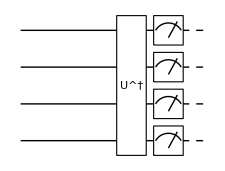

### Example: Measurement of Pauli Z

Consider a qubit is in the state

ψ=0 c_0+1 c_1 .

By default, a measurement is assumed to be in the computational basis and the measurement statistics reflect the probability distribution

P_0=(|c_0|)^2  and  P_1=(|c_1|)^2

as illustrated in the demonstration below.

```mathematica
ket=Ket[]c[0]+Ket[S->1]c[1];
ket//LogicalForm
```

c_0 0_S+c_1 1_S

```mathematica
MeasurementOdds[ket,S[3]]
```

<|0→{(|c_0|)^2/((|c_0|)^2+(|c_1|)^2),c_0 ␣},1→{(|c_1|)^2/((|c_0|)^2+(|c_1|)^2),c_1 1_S}|>

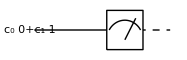

```mathematica
qc=QuantumCircuit[ket,"Spacer",Measurement[S[3]],"PortSize"->{2,0.2}]
```

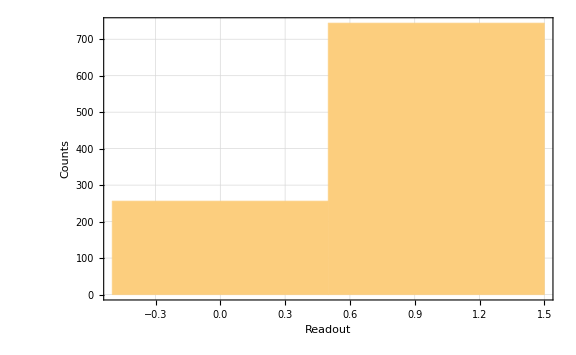

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;
data=Table[ExpressionFor[qc];Readout@S[3],1000];Histogram[data,FrameLabel->{"Readout","Counts"}]]
```

### Example: Measurement of Pauli X

Next, suppose that we want to make a measurement, this time, in the basis of eigenvectors ± of the Pauli X operator. In this case, it is the Hadamard gate that gives the desired basis change. In the new basis, the state vector |ψ⟩ is given by

ψ=+(c_0+c_1)/(√2)+-(c_0-c_1)/(√2) .

In this case, the measurement statistics are thus in accordance with the probability distribution

P_±=(|c_0+c_1|)^2/2.

```mathematica
MeasurementOdds[ket,S[1]]//Map[Simplify]//LogicalForm
```

<|0→{(|c_0+c_1|)^2/((|c_0-c_1|)^2+(|c_0+c_1|)^2),1/2 (c_0+c_1) (0_S+1_S)},1→{(|c_0-c_1|)^2/((|c_0-c_1|)^2+(|c_0+c_1|)^2),1/2 (c_0-c_1) (0_S-1_S)}|>

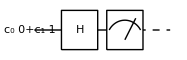

```mathematica
new=QuantumCircuit[ket,S[6],Measurement@S[3],"PortSize"->{2,0.2}]
```

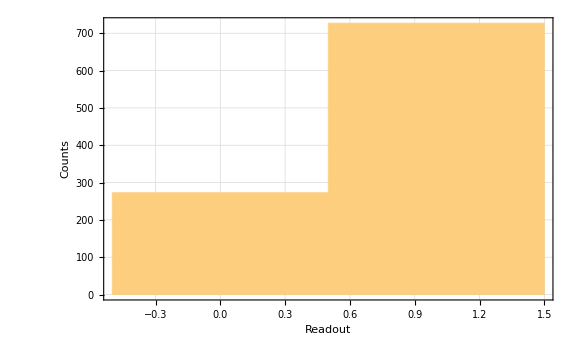

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;data=Table[ExpressionFor[qc];Readout@S[3],1000];Histogram[data,FrameLabel->{"Readout","Counts"}]
]
```

### Example: Bell Measurement

Another interesting example is the Bell measurement. The Bell measurement is a measurement on two qubits in the basis of Bell states,

```mathematica
bs=BellState[S@{1,2}];
bs//LogicalForm//TableForm
```

(0_S_10_S_2+1_S_11_S_2)/(√2)
(0_S_11_S_2+1_S_10_S_2)/(√2)
(0_S_11_S_2-1_S_10_S_2)/(√2)
(0_S_10_S_2-1_S_11_S_2)/(√2)

Note that the Bell states can be generated from the logical basis states by the so-called quantum entangler circuit, a combination of the Hadamard gate and the CNOT gate discussed in Two-Qubit Gates. Therefore, the Bell measurement can be achieved by applying the inverse of the entangling operation.

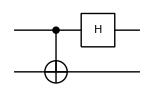

```mathematica
disentangler=QuantumCircuit[CNOT[S[1],S[2]],S[1,6]]
```

Observe that the disentangler quantum circuit indeed maps the Bell states into the logical basis states.

```mathematica
op=ExpressionFor[disentangler];
bs=BellState@S@{1,2};
Thread[bs->op**bs]//LogicalForm//TableForm
```

(0_S_10_S_2+1_S_11_S_2)/(√2)→0_S_10_S_2
(0_S_11_S_2+1_S_10_S_2)/(√2)→0_S_11_S_2
(0_S_11_S_2-1_S_10_S_2)/(√2)→1_S_11_S_2
(0_S_10_S_2-1_S_11_S_2)/(√2)→1_S_10_S_2

Pauli Measurements

```mathematica
<<Q3`
```

In quantum error-correction codes and stabilizer circuits, one often encounters the so-called Pauli measurements, the measurements of tensor products of the single-qubit Pauli operators.

To be specific, let us consider the measurement of Z⊗Z⊗⋯⊗Z on n qubits; the measurement of general Pauli operators can be achieved by incorporating the trick of basis change discussed above and introducing ancillary qubits.

Before going further, it is important to note that the measurement of Z⊗Z⊗⋯⊗Z is a collective measurement and must be distinguished from the sequential measurements of Z on individual qubits. For example, when an even number of qubits are prepared in quantum state

ψ=00…0 c_0+11…1 c_1 ,

the measurement of Z⊗Z⊗⋯⊗Z always gives outcome 1 (out of two eigenvalues ±1 of the observable), and the quantum state remains intact even after the measurement. On the other hand, the measurement of Z, say, on the first qubit produces outcome 0 or 1 (respectively corresponding to eigenvalues ±1 of Z), and the quantum state accordingly collapses to either 00…0 or 11…1.

The measurement of Z⊗Z⊗⋯⊗Z can be implemented within the quantum circuit model of quantum computation by using an ancillary qubit initialized in state |0⟩ and by coupling the qubits in the native register to the ancillary qubits as follows

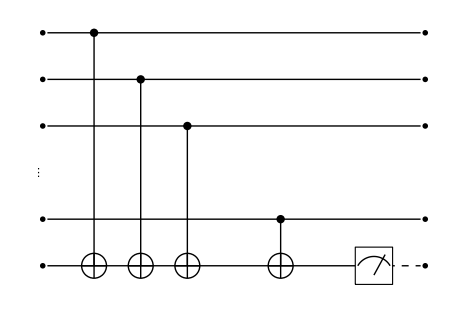

The CNOT gates transform the state of the ancillary qubit from the initial state 0 to the final state x_1⊕x_2⊕⋯⊕x_n involving the logical values of the n qubits in the native register, and hence a simple measurement on the ancillary qubits in the computational basis leads to the desired result.

```mathematica
$n=3;
kk=Range[$n];
Let[Qubit,S,T]
```

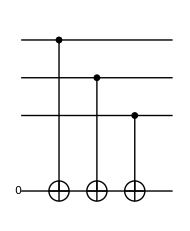

```mathematica
cc=Table[CNOT[S[k],T],{k,$n}];
qc=QuantumCircuit[Ket[T],Sequence@@cc,"Invisible"->S[$n+1/2]]
```

```mathematica
in=Basis[S[kk]];
out=qc**in;
SimpleForm[Thread[in->out],{S[kk],T}]//TableForm
```

000;0→000;0
001;0→001;1
010;0→010;1
011;0→011;0
100;0→100;1
101;0→101;0
110;0→110;0
111;0→111;1

More sophisticated measurements may also be necessary for fast quantum algorithms and quantum error corrections. A common example is the quantum phase estimation, which is one of the core parts of the quantum factorization algorithm.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Measurements on Quantum States
▪Quantum Phase Estimation
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).